So I think everything is good to go for the kappa Barbosa. Let’s do one of the integrals.

Here’s the wrong version

```mathematica
(*a=ToExpression["1 + \\alpha^2 v_b^2 + 2 \\alpha (1-\\alpha) v_b x",TeXForm]*)
```

1+α^2 v_b^2+2 x v_b α[1-α]

Here’s the right version

```mathematica
(*a=ToExpression["\\alpha ( 1 - \\alpha) x^2 + 2 \\alpha(1-\\alpha)v_b x + \\alpha^2 v_b^2 + 1",TeXForm]*)
```

1+α^2 v_b^2+x^2 α[1-α]+2 x v_b α[1-α]

```mathematica
ClearAll["Global`*"]
```

### Try to integrate the first term in the integrand η(α,v_b')

```mathematica
(*Integrate[a^(-κ+1/2),{x,-Subscript[v, b],∞},Assumptions->{0≤ α≤ 1,κ≥ 1.5,Subscript[v, b]≥0}] *)
```

Integrate[(1+α^2 v_b^2+x^2 α[1-α]+2 x v_b α[1-α])^(1/2-κ),{x,-v_b,∞},Assumptions→{0≤α≤1,κ≥1.5,v_b≥0}]

Hmmm … nothin’ doin

```mathematica
(*Integrate[a^(-κ+1/2),{x,-Subscript[v, b],∞},Assumptions->{0≤ α≤ 1,κ≥ 1.5,Subscript[v, b]≥0}] *)
```

How about we take a look at the integrand?

```mathematica
a=.
a[x_,b_,vbprime_]:=1+b^2 vbprime^2+b (1-b) x^2+2 b (1-b)vbprime x
```

```mathematica
anew[x_]:=1+α^2 Subscript[v, b]^2+x^2 α(1-α)+2 x Subscript[v, b] α(1-α)
```

```mathematica
aNegkappaPlusOneHalf[x_,κ_,b_,vbprime_] := (a[x,b,vbprime])^(-κ+1/2)
```

```mathematica
etaCoeff[κ_,b_,vbprime_] :=2/(√Pi)vbprime (1-b) (1/2 Gamma[κ-1/2]/Gamma[κ+1]+vbprime/(√Pi κ) Hypergeometric2F1[0.5,κ,1.5,-vbprime^2])^-1
```

```mathematica
etaintegrand1[x_,κ_,b_,vbprime_] := (√Pi)/(2 √(1-b)) Gamma[κ-1/2]/Gamma[κ] aNegkappaPlusOneHalf[x,κ,b,vbprime]
etaintegrand2[x_,κ_,b_,vbprime_] := x (a[x,b,vbprime]^-κ)Hypergeometric2F1[0.5,κ,1.5,-(b x^2)/a[x,b,vbprime]]
etaintegrand[x_,κ_,b_,vbprime_] := etaintegrand1[x,κ,b,vbprime]-etaintegrand2[x,κ,b,vbprime]
```

### Plot the first term in η(α,v_b') since we can’t analytically integrate it

```mathematica
α = 1/30;
```

```mathematica
Subscript[v, b]=3;
```

```mathematica
etaCoeff[1000,α,Subscript[v, b]]
```

103440.

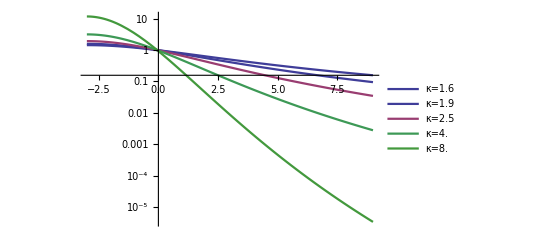

```mathematica
Show[Table[LogPlot[Legended[aNegkappaPlusOneHalf[x,κ,α,Subscript[v, b]],StringForm["κ=`1`",NumberForm[κ,2]]],{x,-Subscript[v, b],3*Subscript[v, b]},PlotStyle->ColorData[1][κ],PlotRange->{All,12},PlotLegends->LineLegend[Automatic]],{κ,{1.6,1.9,2.5,4.0,8.0}}]]
```

See vals

```mathematica
(*(Map[anew,Range[-Subscript[v, b],10 Subscript[v, b],0.1 Subscript[v, b]]])^(-8+1/2)*)
```

Should work, but doesn’t

```mathematica
(*Plot[Evaluate@Table[anewkappa[x,kappa],{kappa,{1.6,1.9,2.5,4.0,8.0}}],{x,-Subscript[v, b],3*Subscript[v, b]},PlotRange->{All,12},PlotLegend->{1.6,1.9,2.5,4.0,8.0},LegendPosition->{0.95,0.05}]*)
```

### Numerically integrate the first term

```mathematica
kappaList={1.6,1.9,2.5,4.0,8.0}
```

{1.6,1.9,2.5,4.,8.}

```mathematica
kappaList=Range[1.6,20,0.1];
```

```mathematica
Table[NIntegrate[aNegkappaPlusOneHalf[x,κ,α,Subscript[v, b]],{x,-Subscript[v, b],∞}],{κ,{1.6,1.9,2.5,4.0,8.0}}]
```

{9.41191,7.99175,7.16165,7.96019,18.9382}

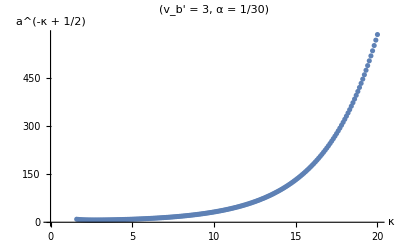

```mathematica
ListPlot[Table[{κ,NIntegrate[aNegkappaPlusOneHalf[x,κ,α,Subscript[v, b]],{x,-Subscript[v, b],∞}]},{κ,kappaList}],PlotLabel->StringForm["(v_b' = ``, α = ``)",Subscript[v, b],α],AxesLabel->{κ,StringForm["a^(-κ + 1/2)"] }]
```

### Numerically integrate the first term PLUS coefficient

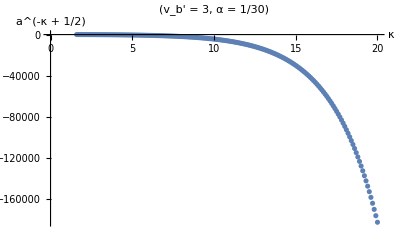

```mathematica
ListPlot[Table[{κ,etaCoeff[κ,α,Subscript[v, b]]* NIntegrate[etaintegrand2[x,κ,α,Subscript[v, b]],{x,-Subscript[v, b],∞}]},{κ,kappaList}],PlotLabel->StringForm["(v_b' = ``, α = ``)",Subscript[v, b],α],AxesLabel->{κ,StringForm["a^(-κ + 1/2)"] }]
```

```mathematica
Hypergeometric2F1[0.5,20,1.5,-Subscript[v, b]^2]
```

0.0673271

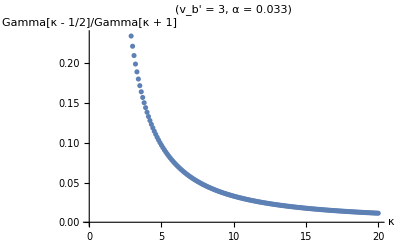

```mathematica
ListPlot[Table[{κ,Gamma[κ-1/2]/Gamma[κ+1]},{κ,kappaList}],PlotLabel->StringForm["(v_b' = ``, α = ``)",Subscript[v, b],NumberForm[N[α],2]],AxesLabel->{κ,StringForm["Gamma[κ - 1/2]/Gamma[κ + 1]"] }]
```

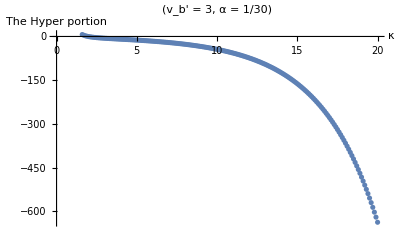

```mathematica
ListPlot[Table[{κ,NIntegrate[etaintegrand2[x,κ,α,Subscript[v, b]],{x,-Subscript[v, b],∞}]},{κ,kappaList}],PlotLabel->StringForm["(v_b' = ``, α = ``)",Subscript[v, b],α],AxesLabel->{κ,StringForm["The Hyper portion"] }]
```

```mathematica
ListPlot[Table[{κ,etaCoeff[κ,α,Subscript[v, b]]* NIntegrate[etaintegrand2[x,κ,α,Subscript[v, b]],{x,-Subscript[v, b],∞}]},{κ,kappaList}],PlotLabel->StringForm["(v_b' = ``, α = ``)",Subscript[v, b],α],AxesLabel->{κ,StringForm["a^(-κ + 1/2)"] }]
```